```mathematica
ClearAll["Global`*"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
```

```mathematica
system=GetNDSolveProblem["VanderPol"]
time={T,0,10};
```

NDSolveProblem[{{Y_1'[T]==Y_2[T],(3 Y_2'[T])/1000==-Y_1[T]+(1-Y_1[T]^2) Y_2[T]},{Y_1[0]==2,Y_2[0]==0},{Y_1[T],Y_2[T]},{T,0,5/2},{},{},{}}]

```mathematica
NDSolve[system,time,Method->"Extrapolation"]
```

NDSolve::ndstf: At T == 0.0223269, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

{{Y_1[T]→InterpolatingFunction[…][T],Y_2[T]→InterpolatingFunction[…][T]}}

```mathematica
NDSolve[system,time,Method->"StiffnessSwitching"]
```

{{Y_1[T]→InterpolatingFunction[…][T],Y_2[T]→InterpolatingFunction[…][T]}}

```mathematica
NDSolve[system,time,Method->"ExplicitRungeKutta",AccuracyGoal->5,PrecisionGoal->4]
```

NDSolve::ndstf: At T == 0.0307508, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

{{Y_1[T]→InterpolatingFunction[…][T],Y_2[T]→InterpolatingFunction[…][T]}}

{{Y_1[T]→InterpolatingFunction[…][T],Y_2[T]→InterpolatingFunction[…][T]}}

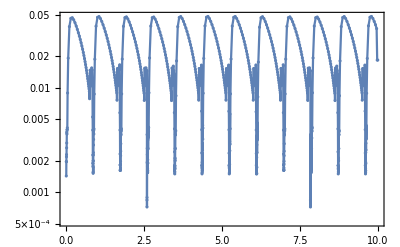

```mathematica
sol=NDSolve[system,time,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->5,PrecisionGoal->4]
StepDataPlot[sol]
```